# Inclined Fusion Pore Energy

Curtis Sera
v1.1.2, 2020-03-11

## Set - up : Establishing the Coordinate System

Let’s try applying the inclined membrane pore solution from Christoph & Rob’s paper.
Adapting it to a bent membrane rather than a bent monolayer, it has the following coordinate scheme:
-Graphics-

First let’s just check that we can get their results in Mathematica to begin with

## Test Application to Published Monolayer Pore Situation

Let' s try to replicate fig 5 from Christoph and Rob' s paper just to verify that things are working

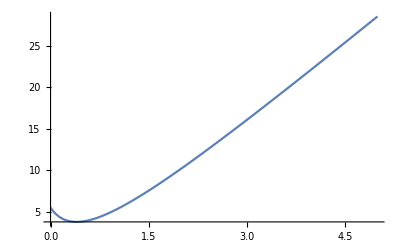

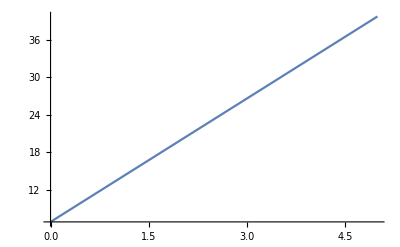

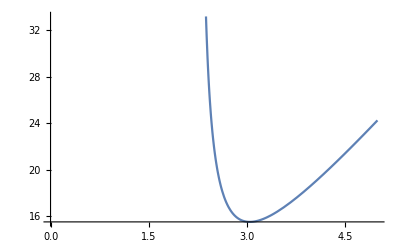

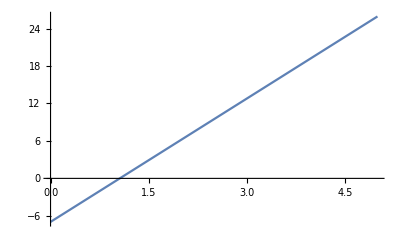

```mathematica
Kb=1; (* kT; Helfrich bending constant *)
H0=0; (* 1/nm; spontaneous curvature *)
h=0.5; (* nm; membrane thickness *)
R1=1.5; (* nm; assume that the membranes are within the critical distance for hemifusion *)
m=h+R1;
R2[r_,ω_,θ_]:=R1 - ((r+m Cos[θ])/(Cos[PlusMinus[Abs[ω],θ]]));

(*ξ[r_,θ_]:=(r+m Cos[θ])/(R1);*) (*Original formula*)
ξ[r_,θ_]:=(r-m+2m Cos[θ])/(R1); (*Adapting original formula to r-rm where rm = m(1-Cos[θ]) *)
W[r_,θ_]:=(2ξ[r,θ]^2)/(Sqrt[ξ[r,θ]^(2)-1]) * (ArcTan[(Sqrt[ξ[r,θ]^(2)-1]* Tan[(θ/2)+(Pi/4)])/(ξ[r,θ]-1)]-ArcTan[(Sqrt[ξ[r,θ]^(2)-1]*Tan[θ/2])/(ξ[r,θ]-1)]);
T[r_,θ_]:=-4 Cos[θ]-H0 R1 (Pi ξ[r,θ] - 4 Cos[θ])+H0^2 R1^2 ((ξ[r,θ] Pi)/2 - Cos[θ]);

G[r_,θ_]:=Pi Kb (W[r,θ]+W[r,-θ]+2 T[r,θ]);
GRim[r_,θ_]:=Pi Kb (Pi ξ[r,θ]-2 Cos[θ]);

x[r_,θ_]:=r-m(1-Cos[θ]);

Plot[G[r,0],{r,0,5}]
Plot[GRim[r,0],{r,0,5}]
Plot[G[r,0.4 Pi],{r,0,5}]
Plot[GRim[r,0.4Pi],{r,0,5}]
```

```mathematica
G[0,0]
G[0.5,0]
G[1,0]
G[5,0]
G[0.5, 0.4 Pi]
G[0,Pi/4]
W[0.5,0.4 Pi]
T[0.5,0.4 Pi]
```

5.50382

3.85234

5.25776

28.5036

-7.83064+0.310406 ⅈ

-20.6445+3.6111 ⅈ

0.0323651+0.0988054 ⅈ

-1.23607

This appears to be happening because the range for ξ is being broken.  Their solution requires ξ > 1, but I’m feeding it conditions where ξ < 1 which is making G complex.  Specifically, the source of the complex component appears to be the W function due to the sqrt[ξ^2 - 1] bits.  This makes sense but is quite confusing given that I’m using the exact conditions they supposedly feed to the solution in fig 5 of their paper...

## Stress of published inclined pore

So I don' t know what' s up with the G for θ < 2 nm, but I’ll go ahead and give the pore E per unit length with what I have for now

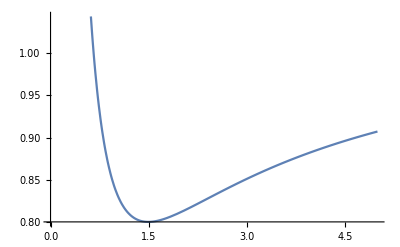

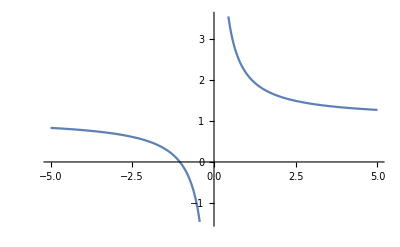

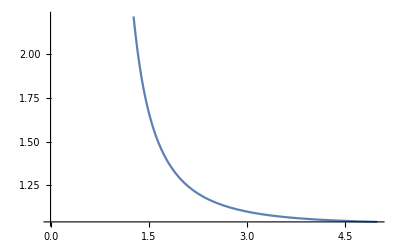

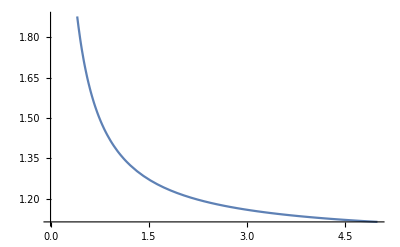

```mathematica
GLength[r_,a_]:=G[r,a]/(2*Pi*r);
GRimLength[r_,a_]:=Grim[r,a]/(2*Pi*r);

Plot[GLength[r,0],{r,0,5}]
Plot[GRimLength[r,0],{r,0,5}]
Plot[GLength[r,0.4 Pi],{r,0,5}]
Plot[GRimLength[r,0.4Pi],{r,0,5}]
```

Fascinating what happens with the total pore pseudo-stress.  This indicates...?  Unlike total pore E for θ = 0 which reaches a minimum at r = ~0.5 nm, the pseudo-stress reaches a minimum at r = ~1.5 nm.  Meanwhile, the rim contribution has gone from linear (G = a r + b) increase to rational (G/r = a + b/r) decay.

## Inclined fusion pore

Ok, well I' m still not sure why I' m getting something different than in fig 5, but I' ll try applying it to a hypothetical fusion pore anyway while I wait for Christoph to give feedback.
First, I’ll read in the relevant parameters based on Aeffner et al’s x-ray diffraction (2012) measurements.  They found that at the hemifusion stalk stage, the hemifused monolayers were separated by ~2 nm (compare to Yang and Huang, 2002 who observed d = 1 nm), the bilayers were ~3 nm thick, and the hemifusion stalk had a minimum diameter of ~2 nm.  So...

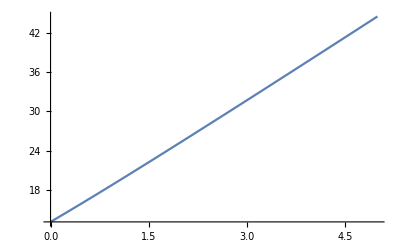

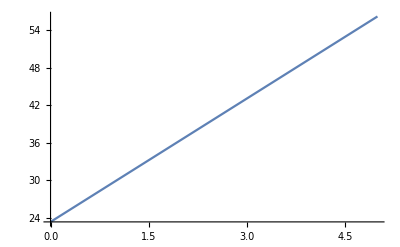

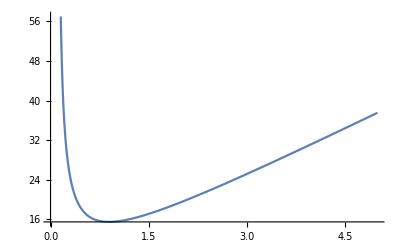

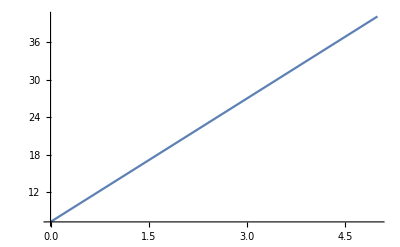

```mathematica
R1Meas=1.5; (* nm; assume that the membranes are within the critical distance for hemifusion *)
hMeas = 3; (* nm; Measured membrane thickness *)

Kb=1; (* kT; Helfrich bending constant *)
H0=0; (* 1/nm; spontaneous curvature *)
m=hMeas+R1Meas;

R2[r_,ω_,θ_]:=R1Meas - ((r+m Cos[θ])/(Cos[PlusMinus[Abs[ω],θ]]));

ξMeas[r_,θ_]:=(r+m Cos[θ])/(R1Meas);
WMeas[r_,θ_]:=(2ξMeas[r,θ]^2)/(Sqrt[ξMeas[r,θ]^(2)-1]) * (ArcTan[(Sqrt[ξMeas[r,θ]^(2)-1]* Tan[(θ/2)+(Pi/4)])/(ξMeas[r,θ]-1)]-ArcTan[(Sqrt[ξMeas[r,θ]^(2)-1]*Tan[θ/2])/(ξMeas[r,θ]-1)]);
TMeas[r_,θ_]:=-4 Cos[θ]-H0 R1Meas (Pi ξ[r,θ] - 4 Cos[θ])+H0^2 R1Meas^2 ((ξMeas[r,θ] Pi)/2 - Cos[θ]);

GMeas[r_,θ_]:=Pi Kb (WMeas[r,θ]+WMeas[r,-θ]+2 TMeas[r,θ]);
GRimMeas[r_,θ_]:=Pi Kb (Pi ξMeas[r,θ]-2 Cos[θ]);

Plot[GMeas[r,0],{r,0,5}]
Plot[GRimMeas[r,0],{r,0,5}]
Plot[GMeas[r,0.4 Pi],{r,0,5}]
Plot[GRimMeas[r,0.4Pi],{r,0,5}]
```